```mathematica
here = NotebookDirectory[];
```

```mathematica
<<(here<>"gEDAmath.m")
```

Basic linear triode model.

```mathematica
fet[options___][refdes_]:=modeleqs[refdes,i["D"]==value(v["G"]-v["S"]),i["G"]==0,i["S"]+i["D"]==0]/.{options}/.{value->gm}
```

Current source model.

```mathematica
current[options___][refdes_]:={i[refdes,"1"]==value}/.{options}/.value->iin
```

Import the "netlist".

```mathematica
<<(here<>"parlowmath.m")
```

in->out transfer function:

```mathematica
tf=Simplify[transferFunction[in,out]]/.stim->0
```

(2 bw π (gm-cgd s) (1+cout rout s))/(2 bw π (gm-cgd s) (1+cout rout s)+s^2 (cout+cgs cout rop s+cgd (1+cout rop s+cout rout s+cgs rop s (1+cout rout s)+gm (rop+cout rop rout s))))

Check for gain of 1 at DC.

```mathematica
tf/.s->0
```

1

Output impedance:

```mathematica
zf=Simplify[transferFunction[-stim,out]]/.in->0
```

(s (1+cgd rop s+cgs rop s) (1+cout rout s))/(2 bw π (gm-cgd s) (1+cout rout s)+s^2 (cout+cgs cout rop s+cgd (1+cout rop s+cout rout s+cgs rop s (1+cout rout s)+gm (rop+cout rop rout s))))

Output impedance approaches zero at DC:

```mathematica
zf/.s->0
```

0

Units are MHz, nF, kΩ, μs, mS.

bw->0.2 MHz		Opamp gain-bandwith product
rop->1.0 kΩ		Opamp open loop output resistance
cgs->0.265 nF		FET gate-source capacitance
cout->22000		Use 22 μF

```mathematica
devpar={bw->0.2,rop->1.0,cgs->0.265,cout->22000}
```

{bw→0.2,rop→1.,cgs→0.265,cout→22000}

Measured transconductance of the composite FET is 2000 mS  at 1 A. For the high current case, assume 0.1 A. The LM195 is active, reducing the effective cgd.

```mathematica
hicurr={gm->2000Sqrt[0.1],cgd->0.02}
```

{gm→632.456,cgd→0.02}

Given lists of parameters, extract "natural frequencies".

```mathematica
natfreqs[p___]:=s/.Solve[Denominator[zf/.devpar/.Flatten[{p}]]==0,s]
```

Stability index: range is -1 to 1. 1 is the most stable. Negative numbers are unstable.

```mathematica
stability[z_]:=-Re[z]/Abs[z]
SetAttributes[stability,Listable]
```

```mathematica
natfreqs[hicurr,rout->0.005]
```

{-13142.3,-1.43133-3.05539 ⅈ,-1.43133+3.05539 ⅈ,-0.00911175}

```mathematica
stability[%]
```

{1.,0.424217,0.424217,1.}

```mathematica
locurr={gm->2000Sqrt[0.001],cgd->0.05}
```

{gm→63.2456,cgd→0.05}

```mathematica
natfreqs[locurr,rout->0.005]
```

{-4994.14,-2.55287,-0.459485,-0.0093083}

```mathematica
speed[r_]:=-Re[natfreqs[hicurr,rout->r]][[3]]
```

```mathematica
stab[r_]:=Min@@Flatten[{stability[natfreqs[hicurr,rout->r]],stability[natfreqs[locurr,rout->r]]}]
```

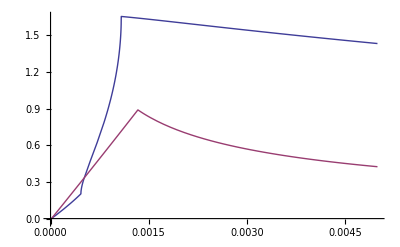

```mathematica
Plot[{speed[r],stab[r]},{r,0,0.005}]
```

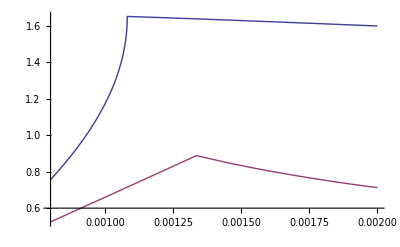

```mathematica
Plot[{speed[r],stab[r]},{r,0.0008,0.002}]
```

```mathematica
pstep[tf_,d_]:=With[{sr=stepResponse[tf,2d,d/1000]},Plot[Evaluate[sr-(sr/.t->d)],{t,0,d}]]
```

```mathematica
natfreqs[hicurr,rout->0.0013]
```

{-43751.4,-1.64142-0.783768 ⅈ,-1.64142+0.783768 ⅈ,-0.0362218}

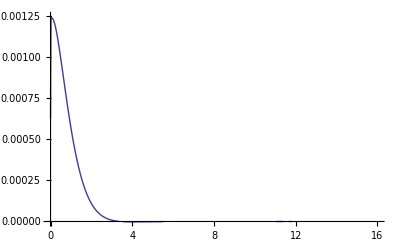

```mathematica
pstep[zf/.devpar/.hicurr/.rout->0.0013,16]
```

```mathematica
natfreqs[hicurr,rout->0.0005]
```

{-109934.,-2.99254,-0.306986,-0.134983}

```mathematica
natfreqs[hicurr,rout->0.001]
```

{-56160.7,-2.14049,-1.17259,-0.048356}

```mathematica
natfreqs[hicurr,rout->0.002]
```

{-29274.,-1.60055-1.577 ⅈ,-1.60055+1.577 ⅈ,-0.0230596}

```mathematica
FindRoot[natfreqs[hicurr,rout->r][[2]]==natfreqs[hicurr,rout->r][[3]],{r,0.002}]
```

{r→0.00108159+1.09236×10^-16 ⅈ}

```mathematica
natfreqs[hicurr,rout->0.0010815873028813224]
```

{-52104.4,-1.65276-5.72361×10^-7 ⅈ,-1.65276+5.72361×10^-7 ⅈ,-0.0442776}

```mathematica
stability[%]
```

{1.,1.,1.,1.}

```mathematica
natfreqs[hicurr,r1->10,r3->0,r4->0.005,c2->10000,c1->1]
```

{-2.08004-3.92542 ⅈ,-2.08004+3.92542 ⅈ,-0.0687575,-0.0221017}

```mathematica
stability[%]
```

{0.468218,0.468218,1.,1.}

```mathematica
natfreqs[hicurr,r1->10,r3->0,r4->0.0036,c2->10000,c1->1]
```

{-2.08136-3.34888 ⅈ,-2.08136+3.34888 ⅈ,-0.0481898,-0.0400305}

```mathematica
stability[%]
```

{0.527866,0.527866,1.,1.}

```mathematica
natfreqs[locurr,r1->10,r3->0,r4->0.0036,c2->10000,c1->1]
```

{-2.11434-1.27828 ⅈ,-2.11434+1.27828 ⅈ,-0.0111298-0.0191684 ⅈ,-0.0111298+0.0191684 ⅈ}

```mathematica
stability[%]
```

{0.85576,0.85576,0.502125,0.502125}

```mathematica
natfreqs[hicurr,r1->10,r3->0,r4->0.0027,c2->22000,c1->1.2]
```

{-2.08582-2.92255 ⅈ,-2.08582+2.92255 ⅈ,-0.041291,-0.021341}

```mathematica
stability[%]
```

{0.618533,0.618533,1.,1.}

```mathematica
natfreqs[locurr,r1->10,r3->0,r4->0.0027,c2->22000,c1->1.2]
```

{-2.11023-1.1639 ⅈ,-2.11023+1.1639 ⅈ,-0.0069121-0.0121585 ⅈ,-0.0069121+0.0121585 ⅈ}

```mathematica
stability[%]
```

{0.875642,0.875642,0.494217,0.494217}

```mathematica
Min@@%
```

0.494217

```mathematica
nf[o_,r_,c_]:=(nf[o,r,c]=natfreqs[o,r1->10,r3->0,r4->r,c2->10000,c1->c])
```

```mathematica
nfh[r_,c_]:=nf[hicurr,r,c]
```

```mathematica
nfl[r_,c_]:= nf[locurr,r,c]
```

```mathematica
speed[r_?NumericQ,c_?NumericQ]:=Min@@-Re[nfh[r,c]]
```

```mathematica
speed[0.003,0.9]
```

0.0468382

```mathematica
stab[r_?NumericQ,c_?NumericQ]:=Min@@stability[Join[nfl[r,c],nfh[r,c]]]
```

```mathematica
stab[0.0016,0.25]
```

0.380227

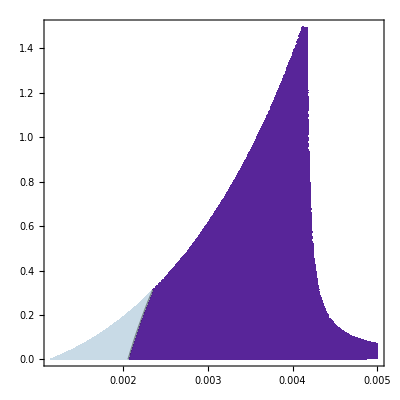

```mathematica
ContourPlot[speed[r4,c1],{r4,0.0,0.005},{c1,0.0,1.5},RegionFunction->Function[{r4,c1,z},stab[r4,c1]>0.5],PlotRange->All]
```

```mathematica
speed[0.0012,0.]
```

0.0919898

```mathematica
stab[0.0012,0.]
```

0.529532

```mathematica
nfh[0.0012,0]
```

{-2.19893,-1.48266,-0.0919898}

```mathematica
nfl[0.0012,0]
```

{-3.67795,-0.0478174-0.0766017 ⅈ,-0.0478174+0.0766017 ⅈ}

```mathematica
natfreqs[hicurr,r1->10,r3->0,r4->0.0012,c2->10000,c1->0]
```

{-2.19893,-1.48266,-0.0919898}

```mathematica
natfreqs[locurr,r1->10,r3->0,r4->0.0012,c2->10000,c1->0]
```

{-3.67795,-0.0478174-0.0766017 ⅈ,-0.0478174+0.0766017 ⅈ}

Now put in a little cgd (20 pF).

```mathematica
devpar={bw->0.2,rout->1.0,cgs->0.265,cgd->0.02}
```

{bw→0.2,rout→1.,cgs→0.265,cgd→0.02}

```mathematica
natfreqs[hicurr,r1->10,r3->0,r4->0.0012,c2->10000,c1->0]
```

{-22199.,-1.37493-0.74751 ⅈ,-1.37493+0.74751 ⅈ,-0.0919361}

No serious problem from cgd, given that the LM195 reduces its effect.

For locurr, effective cgd may be higher.

```mathematica
devpar={bw->0.2,rout->1.0,cgs->0.265,cgd->0.05}
```

{bw→0.2,rout→1.,cgs→0.265,cgd→0.05}

```mathematica
natfreqs[locurr,r1->10,r3->0,r4->0.0012,c2->10000,c1->0]
```

{-20050.7,-3.04181,-0.047823-0.0768672 ⅈ,-0.047823+0.0768672 ⅈ}

Almost no effect  here.

```mathematica
devpar={bw->0.2,rout->1.0,cgs->0.265,cgd->0.02}
```

{bw→0.2,rout→1.,cgs→0.265,cgd→0.02}

```mathematica
natfreqs[hicurr,r1->10,r3->0,r4->0.0018,c2->10000,c1->0]
```

{-32261.4,-1.59755-1.38243 ⅈ,-1.59755+1.38243 ⅈ,-0.0578567}

My interpretation here is that the second/third natural frequency will be the most visible: the last just reflects the recharge of the capacitor at ~constant output voltage. Therefore, I like this solution. It's very stable, and it's fast: 0.6 μs time constant at high current, 14μs at low current.

```mathematica
stability[%]
```

{1.,0.756185,0.756185,1.}

```mathematica
devpar={bw->0.2,rout->1.0,cgs->0.265,cgd->0.05}
```

{bw→0.2,rout→1.,cgs→0.265,cgd→0.05}

```mathematica
natfreqs[locurr,r1->10,r3->0,r4->0.0018,c2->10000,c1->0]
```

{-30113.2,-3.33434,-0.0734279-0.0539018 ⅈ,-0.0734279+0.0539018 ⅈ}

```mathematica
stability[%]
```

{1.,1.,0.806119,0.806119}

```mathematica
devpar={bw->0.2,rout->1.0,cgs->0.265,cgd->0.02}
```

{bw→0.2,rout→1.,cgs→0.265,cgd→0.02}

```mathematica
natfreqs[hicurr,r1->10,r3->0,r4->0.0018,c2->22000,c1->0]
```

{-32261.4,-1.61251-1.40181 ⅈ,-1.61251+1.40181 ⅈ,-0.0257112}

```mathematica
stability[%]
```

{1.,0.754692,0.754692,1.}

```mathematica
devpar={bw->0.2,rout->1.0,cgs->0.265,cgd->0.05}
```

{bw→0.2,rout→1.,cgs→0.265,cgd→0.05}

```mathematica
natfreqs[locurr,r1->10,r3->0,r4->0.0018,c2->22000,c1->0]
```

{-13446.9,-2.96922,-0.116342,-0.0326084}

Raising the cap to 22 μF has almost no effect on the high current case, but improves speed and damping in the low current case.

Bottom line:
Eliminate, R1, C1, R3. 
C2->22μF
R4->1.8 ohm